# 深入理解数值计算

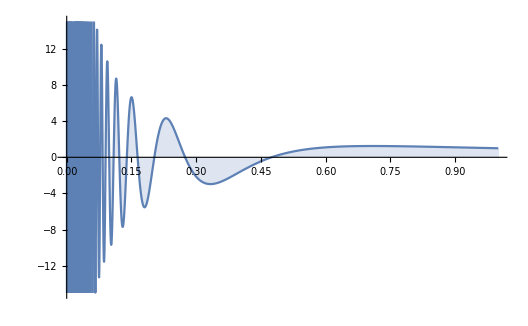
## 具体应用和高级技术指南 Wolfram 语言专题讲座系列 -Graphics- 杨圣汇 Wolfram Research training@wolfram.com

目录

数值函数

概述和应用

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

数值函数

概述和应用

积分

微分方程

代数方程数值解

最优化问题

线性代数和稀疏矩阵

## 数值积分：求积

NIntegrate 计算给定函数的数值积分结果 (“numerical quadrature”):

```mathematica
NIntegrate[2 √(1-y^2),{y,-1,1}]
```

3.14159

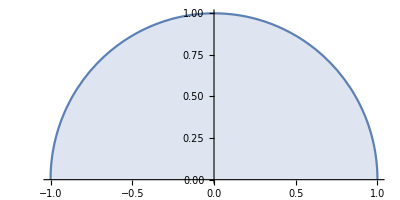

```mathematica
Plot[√(1-y^2),{y,-1,1},Filling->Axis,AspectRatio->Automatic]
```

## 数值积分: 列表积分

对于一系列点的积分计算，首先使用插值函数

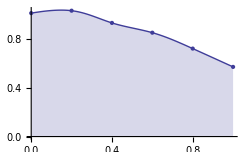

```mathematica
y={{0,1.01},{0.2,1.03},{0.4,0.93},{0.6,0.85},{0.8,0.72},{1,0.57}};
```

```mathematica
f=Interpolation[y];
```

下一步使用 NIntegrate:

```mathematica
NIntegrate[f[t],{t,0,1}]
```

0.868917

```mathematica
Clear[f]
```

## 数值积分: 路径积分

参数化路径.

```mathematica
path[t_]:=2+Exp[ⅈ t]
```

```mathematica
f[z_]:=Sin[z]/(z-2)^3
```

路径积分:

```mathematica
Chop@NIntegrate[f[path[t]] path'[t],{t,0,2π}]
```

0.-2.85664 ⅈ

```mathematica
2π ⅈ Residue[f[t],{t,2}]//N
```

0.-2.85664 ⅈ

## 数值积分: 向量微积分

曲面积分，体积计算以及向量微积分

参数化曲面:

```mathematica
{x,y,z}={(2+Cos[v])Cos[u],(2+Cos[v])Sin[u],Sin[v](5/4-Cos[u])};
```

```mathematica
ParametricPlot3D[{x,y,z},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

曲面积分:

```mathematica
NIntegrate[Norm[Cross[D[{x,y,z},u],D[{x,y,z},v]]],{u,0,2π},{v,0,2π}]
```

92.9654

用高斯散度定理计算被曲面包裹区域的体积

```mathematica
NIntegrate[({x,y,z}/3).Cross[D[{x,y,z},u],D[{x,y,z},v]],{u,0,2π},{v,0,2π}]
```

49.348

```mathematica
Clear[x,y,z]
```

## 微分方程

NDSolve 可以求解常微分和偏微分方程

```mathematica
NDSolve[{x''[t]==-x[t],x'[0]==x[0]==1},x,{t,0,10}]
```

{{x→InterpolatingFunction[…]}}

微分方程的解是由 Rule/规则 构成的列表

```mathematica
solution=x[t]/.First[%]
```

InterpolatingFunction[…][t]

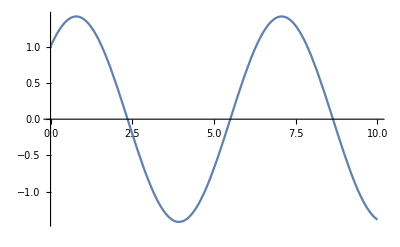

```mathematica
Plot[solution,{t,0,10}]
```

## 微分方程: 特殊类型的常微分方程

NDSolve 可以求解延迟微分方程和微分-代数方程

有延迟项的微分方程:

```mathematica
{x[t],x'[t]}/.First[NDSolve[{x'[t]==x[t](x[t-Pi]-x'[t-1]),x[t/;t≤0]==Cos[t]},x,{t,0,5}]]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

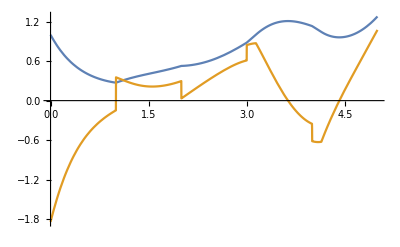

```mathematica
Plot[%,{t,0,5}]
```

## 微分方程: 偏微分方程

薛定谔方程:

```mathematica
equations={ⅈ D[ψ[x,t],t]==-1/2 D[ψ[x,t],{x,2}]+250Sin[x/2]^10ψ[x,t],ψ[x,0]==Exp[ⅈ 20 x]Exp[-10x^2],ψ[-π,t]==ψ[π,t]};
```

```mathematica
sol=ψ/.First[NDSolve[equations,ψ,{x,-π,π},{t,0,0.4}]]
```

InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 0.4}}, <>]

在周期势井中量子的往复运动:

```mathematica
Animate[Plot[{Sin[x/2]^10+Abs[sol[x,t]]^2,Sin[x/2]^10},{x,-π,π},PlotRange->{0,3/2},Filling->1->{2}],{t,0,0.4},DefaultDuration->10]
```

## 微分方程: 不定积分

NDSolve 来计算不定积分.

f(x)==∫_0^x sin(exp(t))ⅆt=="?"

把不定积分转换为微分方程:

```mathematica
f=y/.First[NDSolve[{y'[x]==Sin[Exp[x]],y[0]==0},y,{x,0,3}]]
```

InterpolatingFunction[…]

绘制积分和积分因子:

```mathematica
Animate[Plot[{f[x],Sin[Exp[x]]},{x,0,t},Filling->{2->Axis},PlotStyle->{Thick,None},PlotRange->{{0,3},{-1,1}}],{t,0,3}]
```

## 求解方程

FindRoot 可以用数值方法求解一个或者多个方程的根.

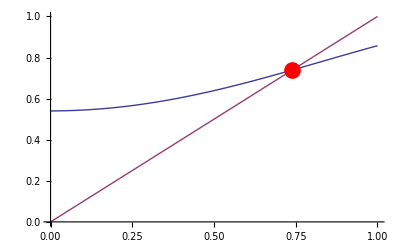

```mathematica
FindRoot[Cos[Cos[x]]==x,{x,0}]
```

## 求解方程

FindRoot 来找到反函数.

给定 y(x), 试求它的反函数 inv(t):

```mathematica
y[x_]:=x^x+x
```

```mathematica
inv[t_]/;NumericQ[t]:=x/.FindRoot[y[x]==t,{x,1}]
```

Use it like any other function:

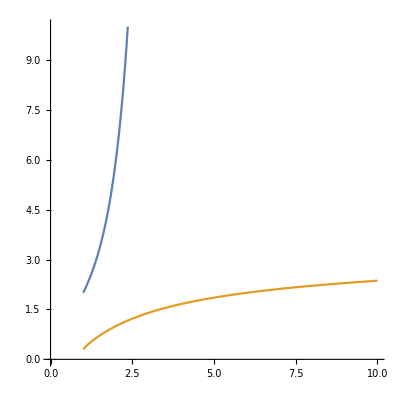

```mathematica
Plot[{y[t],inv[t]},{t,1,10},PlotRange->{0,10},AxesOrigin->{0,0},Axes->True,AspectRatio->1]
```

## 优化问题

约束条件下的局域或者全局优化问题

FindMinimum 寻找局部极小值:

```mathematica
FindMinimum[Exp[-x^2] Cos[5Exp[x]],{x,1}]
```

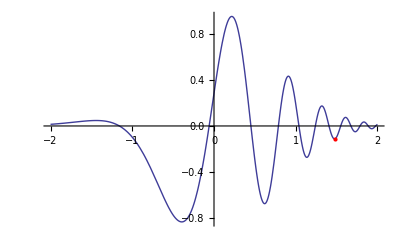

NMinimize 试图找到全局最小值:

```mathematica
NMinimize[Exp[-x^2] Cos[5Exp[x]],x]
```

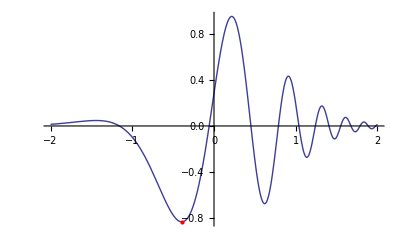

## 优化问题

高维受约束的优化问题:

```mathematica
NMinimize[{Sin[x]Cos[2y+1],x^4+y^2<3},{x,y}]
```

-Graphics3D-

## 线性代数: 求解线性方程组

LinearSolve 在很多方程求解的过程中起到非常重要的作用

精确数组成的数组  (Mathematica 8 开始就有深度优化):

```mathematica
LinearSolve[({{0, 2, 9, 0}, {1, 8, 7, 0}, {8, 2, 0, 0}, {5, 0, 0, 1}}),({{5}, {3}, {3}, {3}})]
```

也可以求解机器精度的数组构成的线性方程组:

```mathematica
LinearSolve[RandomReal[1,{20,20}],RandomReal[1,{20}]]
```

## 线性代数: 常用操作

所有常用线性代数相关操作均可使用，包括了:

```mathematica
LeastSquares[RandomReal[1,{100,20}],RandomReal[1,{100}]]
```

```mathematica
Eigenvalues[RandomReal[1,{10,10}]]
```

## 线性代数: 稀疏矩阵

快速有效的表达稀疏矩阵

```mathematica
SparseArray[{{4,2}|{3,6}->4,{i_,i_}->2},{8,8}]
```

SparseArray[…]

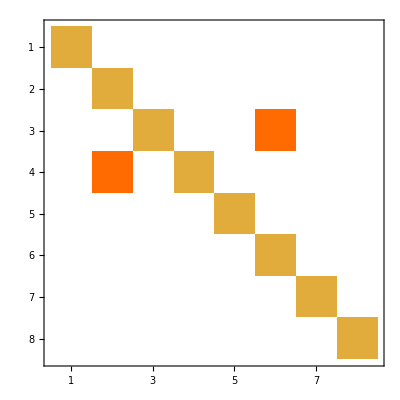

```mathematica
MatrixPlot[%]
```

## 线性代数: 稀疏矩阵

离散化 2 维网格得到线性方程:

(∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)==q"⟹"(u_(i-1,j)-2 u_(i,j)+u_(i+1,j))+(u_(i,j-1)-2 u_(i,j)+u_(i,j+1))==q

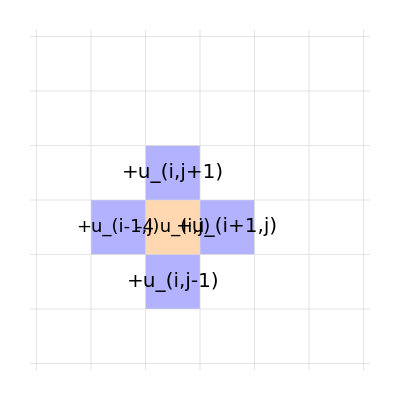

用稀疏矩阵表示线性方程:

```mathematica
n=30;
```

```mathematica
eqns=N[SparseArray[{{i_,j_,i_,j_}->-4,{i_,j1_,i_,j2_}/;Abs[j1-j2]==1->1,{i1_,j_,i2_,j_}/;Abs[i1-i2]==1->1},{n,n,n,n}]]
```

```mathematica
eqns=Flatten[eqns,{{1,2},{3,4}}]
```

线性方程组的结构:

```mathematica
MatrixPlot[eqns]
```

热源:

```mathematica
source=ImageData[ColorConvert[ImageResize[ImageCrop[Rasterize["8",ImageSize->n]],{n,n}],"Grayscale"]]-1;
```

```mathematica
ArrayPlot[source,ImageSize->Small]
```

求解线性方程组:

```mathematica
sol=LinearSolve[eqns,Flatten[source]];
```

```mathematica
ListPlot3D[Partition[sol,n]]
```

数值方法

算法控制详解

-Graphics- | -Graphics-
-Graphics- | -Graphics-

数值方法

算法控制详解

指定方法

使用更为高级的运算选项

监视算法性能和中间过程

## 指定计算方法

需要调试的情况： 比较各类方法的优缺点 或者 已经知道最优方案

自适应蒙特卡罗方法:

```mathematica
NIntegrate[Boole[x^2+y^2<1],{x,-1,1},{y,-1,1},Method->"AdaptiveMonteCarlo",PrecisionGoal->2]
```

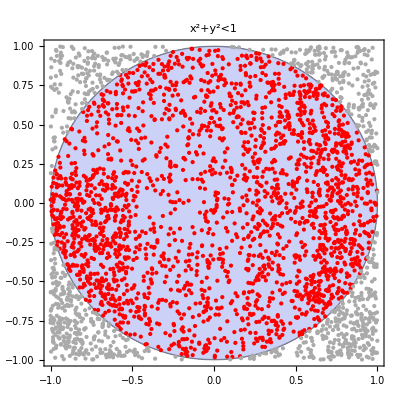

## 指定计算方法

对于大型稀疏矩阵比较直接计算方法和迭代方法:

```mathematica
m=SparseArray[{Band[{1,1}]->RandomReal[{1,1},10^5],Band[{1,2}]->2,Band[{2,1}]->2},{10^5,10^5}]
```

SparseArray[<299998>, {100000, 100000}]

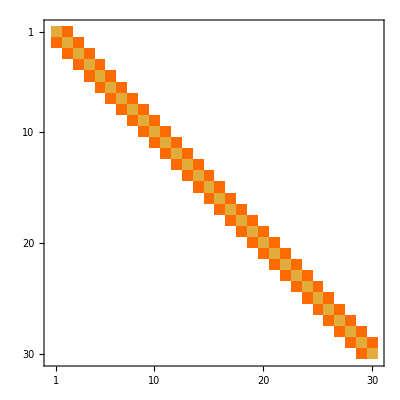

```mathematica
MatrixPlot[Take[m,30,30]]
```

```mathematica
b=RandomReal[1,10^5];
```

迭代法:

```mathematica
Timing[LinearSolve[m,b,Method->"Krylov"];]
```

{0.046875,Null}

直接计算:

```mathematica
Timing[LinearSolve[m,b,Method->"Multifrontal"];]
```

{0.171875,Null}

## 指定计算方法

使用可以在刚性和非刚性的情况下自动切换的数值方法:

```mathematica
Clear [x,y]
```

```mathematica
{x[t],y[t]}/.First[NDSolve[{x'[t]==y[t],(3 y'[t])/1000==-x[t]+(1-x[t]^2)y[t]+Sin[10t],x[0]==2,y[0]==0},{x,y},{t,0,10},Method->"StiffnessSwitching"]]
```

```mathematica
Plot[%,{t,0,10}]
```

## 高级求解器方法: 次级方法和选项设置

参照高级数值方法教程.

Submethods: 总体区域分割和积分策略:

```mathematica
NIntegrate[Sin[10Sin[x]x],{x,0,10},Method->{"LocalAdaptive",Method->"ClenshawCurtisRule"}]
```

Options: 从更大的点数寻找可能的最小值

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"RandomSearch","SearchPoints"->250}]
```

-Graphics3D-

## 高级求解器方法: 特殊方法

有些方法可以得到额外计算分析或者改变解的形式

案例: 高度 h(x) 的位置发射炮弹的落点:

```mathematica
h[x_]:=5+Cos[x/20]+(3Cos[x/3])/(2+Sin[x/10]);
```

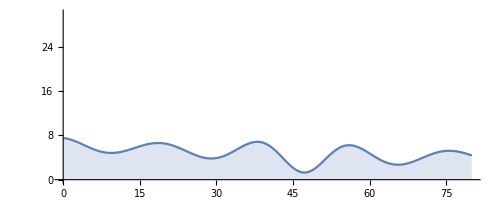

```mathematica
terrain=Plot[h[x],{x,0,80},Filling->0,PlotRange->{0,30},AspectRatio->Automatic,ImageSize->500]
```

初速 s 仰角 θ 考虑空气阻力 drag:

```mathematica
eqn[s_,θ_]:={{p1[0],p2[0]}=={0,h[0]},{p1'[0],p2'[0]}==s{Cos[θ],Sin[θ]},{p1''[t],p2''[t]}==force[{p1'[t],p2'[t]}]}
```

```mathematica
force[v_List]:={0,-9.8}-0.02Norm[v]v
```

EventLocator 在 NDSolve 做碰撞检测:

```mathematica
{p1[t],p2[t]}/.First[NDSolve[eqn[30,45°],{p1[t],p2[t]},{t,0,10},Method->{"EventLocator","Event":>p2[t]==h[p1[t]],"EventAction":>Throw[end=t,"StopIntegration"]}]]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

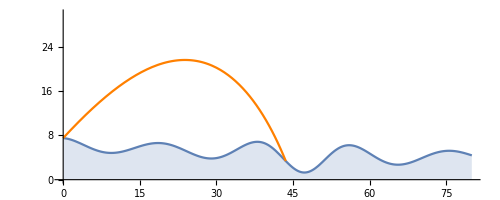

```mathematica
Show[terrain,ParametricPlot[%,{t,0,end},PlotStyle->Orange]]
```

Manipulate 进行互动:

```mathematica
Manipulate[Show[terrain,ParametricPlot[Evaluate[{p1[t],p2[t]}/.First[NDSolve[eqn[s,θ °],{p1[t],p2[t]},{t,0,10},Method->{"EventLocator","Event":>p2[t]==h[p1[t]],"EventAction":>Throw[end=t,"StopIntegration"]}]]],{t,0,end},PlotStyle->Orange]],{{s,40},1,60,Appearance->"Labeled"},{{θ,45},0,90,Appearance->"Labeled"}]
```

NDSolve::deqn: Equation or list of equations expected instead of (ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]))/(2 m))[20.6,1.213] in the first argument (ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]))/(2 m))[20.6,1.213].

ReplaceAll::reps: {(ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]))/(2 m))[20.6,1.213]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParametricPlot::plln: Limiting value end in {t,0,end} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[terrain,ParametricPlot[{p1[t],p2[t]}/.(ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]))/(2 m))[20.6,1.213],{t,0,end},PlotStyle→Orange]].

ParametricPlot::plln: Limiting value end in {t,0,end} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[terrain,ParametricPlot[{p1[t],p2[t]}/.(ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]))/(2 m))[20.6,1.213],{t,0,end},PlotStyle→Orange]].

NDSolve::deqn: Equation or list of equations expected instead of (ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(«1»)[x,y,t]))/(2 m))[20.6,1.213] in the first argument (ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(«1»)[x,y,t]))/(2 m))[20.6,1.213].

ReplaceAll::reps: {(ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 (ψ^(0,2,0)[x,y,t]+ψ^(«1»)[x,y,t]))/(2 m))[20.6,1.213]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParametricPlot::plln: Limiting value end in {t,0,end} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[terrain,ParametricPlot[{p1[t],p2[t]}/.(ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 («1»+«1»))/(2 m))[20.6,«18»],«1»,PlotStyle→«6»]].

ParametricPlot::plln: Limiting value end in {t,0,end} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[terrain,ParametricPlot[{p1[t],p2[t]}/.(ⅈ ℏ ψ^(0,0,1)[x,y,t]==-(ℏ^2 («1»+«1»))/(2 m))[20.6,«18»],«1»,PlotStyle→«6»]].

## 内置算法运行监测: EvaluationMonitor

EvaluationMonitor 可以快速找出算法具体的运算情况:

```mathematica
FindRoot[Cos[x]==x,{x,0},EvaluationMonitor:>Print[x]]
```

0.

1.

0.750364

0.739113

0.739085

0.739085

{x→0.739085}

## 内置算法运行监测: EvaluationMonitor

NIntegrate 在不同区域上的收敛速度:

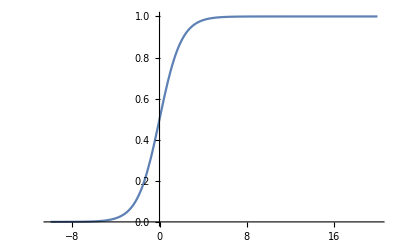

```mathematica
Plot[1/(1+Exp[-x]),{x,-10,20}]
```

Sow 和 Reap 捕捉计算积分采样点的的位置:

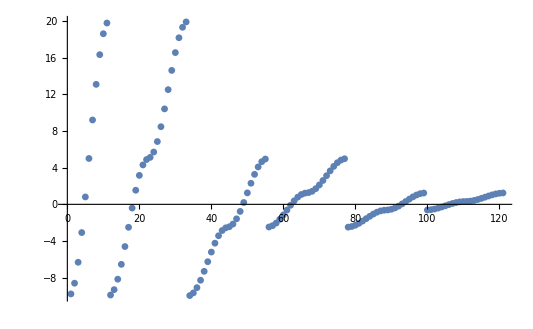

```mathematica
ListPlot[Last@Reap[NIntegrate[1/(1+Exp[-3x]),{x,-10,20},EvaluationMonitor:>Sow[x]]]]
```

另一种可视化这些点的方法:

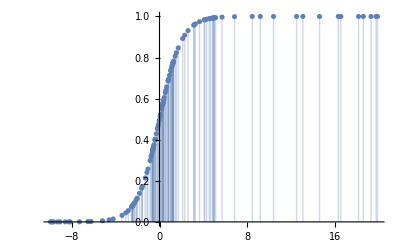

```mathematica
ListPlot[Last@Reap[NIntegrate[1/(1+Exp[-3x]),{x,-10,20},EvaluationMonitor:>Sow[{x,1/(1+Exp[-x])}]]],Filling->Axis]
```

## 内置算法运行监测: StepMonitor

StepMonitor 用来监测算法每个步长之后的进度.

```mathematica
FindMinimum[(1-x)^2+100(-x^2-y)^2+1,{{x,-1.2},{y,1}},StepMonitor:>Print[{x,y}]]
```

## 内置算法运行监测: StepMonitor

StepMonitor 中直接得到解:

```mathematica
Clear[sol]
```

```mathematica
Dynamic[Plot[sol,{x,-10,10},PlotRange->{-5,15},Filling->Axis]]
```

```mathematica
NDSolve[{D[u[t,x], t,t]==D[u[t,x], x,x]+Sin[u[t,x]] ,u[0,x]==ⅇ^(-x^2),Derivative[1,0][u][0,x]==0,u[t,-10]==u[t,10]},u,{t,0,50},{x,-10,10},StepMonitor:>(sol=u[t,x])]
```

Monitor 也可以和进度条一起使用:

```mathematica
Monitor[NDSolve[{D[u[t,x], t,t]==D[u[t,x], x,x]+Sin[u[t,x]] ,u[0,x]==ⅇ^(-x^2),Derivative[1,0][u][0,x]==0,u[t,-10]==u[t,10]},u,{t,0,50},{x,-10,10},StepMonitor:>(sol=u[t,x];progress=t)],ProgressIndicator[progress,{0,50}]]
```

数字

控制精度和准度

数字

控制精度和准度

精确数和近似数

数值函数中的精度目标和准度目标

## 精确数和近似数: 三种精度级别

-Graphics-

## 精确数和近似数: 三种精度级别

内置函数操作一般保留输入的精度属性

精确输入 ⟶ 精确输出

```mathematica
Sqrt[8]
```

```mathematica
Precision[%]
```

任意精度输入 ⟶ 任意精度输出

```mathematica
Sqrt[8`50]
```

```mathematica
Precision[%]
```

机器精度输入 ⟶ 机器精度输出

```mathematica
Sqrt[8.0]
```

```mathematica
Precision[%]
```

## 精确数和近似数: 混合精度

不同精度混合，系统会返回最合理的情况:

```mathematica
8`50+2`25
```

10.

```mathematica
Precision[%]
```

25.699

如果有一部分是 MachinePrecision, 那么结果也是 MachinePrecision :

```mathematica
Sin[5`50]+√6.5
```

```mathematica
Precision[%]
```

## 精确数和近似数: 精度和准度

Precision 有效数字的个数. Accuracy 小数位数.

10 位精度, 低准度:

```mathematica
x=10000000.000`10;
```

```mathematica
{Precision[x],Accuracy[x]}
```

10 位精度, 高准度:

```mathematica
x=0.0000001`10;
```

```mathematica
{Precision[x],Accuracy[x]}
```

## 数值计算相关函数中的精度和准度

函数目标是要么得到指定精度 (PrecisionGoal), 要么得到足够的小数位数 (AccuracyGoal).

7 个有效数字或者 2 两位正确的小数位数:

```mathematica
NIntegrate[Exp[10Sin[x]],{x,0,1},PrecisionGoal->7,AccuracyGoal->2]
```

699.181

```mathematica
{Precision[%],Accuracy[%]}
```

{MachinePrecision,13.11}

## 精确数和近似数: 相对误差

当只需要指定至少 n 个有效数字目标的时候，直接指明 PrecisionGoal 即可

```mathematica
FindRoot[√x==2/x,{x,1,2π},PrecisionGoal->5,AccuracyGoal->∞]
```

{x→1.5874}

## 数值计算函数中的精度和准度目标: 零点

当真实值为零的时候,  PrecisionGoal 不可能成立. 此时必须加入 AccuracyGoal.

```mathematica
NIntegrate[Sin[x],{x,0,2π},PrecisionGoal->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.58957}. NIntegrate obtained 1.23165×10^-16 and 5.52727×10^-16 for the integral and error estimates.

1.23165×10^-16

```mathematica
NIntegrate[Sin[x],{x,0,2π},AccuracyGoal->10,WorkingPrecision->10,PrecisionGoal->10]
```

2.69079205×10^-20

计算技巧

编程和性能测试

-Graphics- | -Graphics-

计算技巧

编程和性能测试

多种数值函数的合并操作

使用内置高效函数运算

数字和数组

编译

## 多种数值函数的合并操作

很多情况下一个数值函数的输出是下一个函数的输入值

数值求解关于参数 a 的微分方程（或者使用 ParametricNDSolve）

```mathematica
Clear[sol,aa,x,y]
```

```mathematica
sol[a_]/;NumericQ[a]:=ParametricNDSolveValue[{y''[x]==-y[x](1+Cos[x+y[x]]),y[0]==1,y'[0]==aa},y,{x,0,10},{aa}][a]
```

```mathematica
sol[5]
```

InterpolatingFunction[…]

根据不同 a 绘制方程的解:

```mathematica
Animate[Plot[Evaluate[sol[a][x]],{x,0,10},PlotRange->4],{a,0,1}]
```

用数值积分的办法来计算关于参数 a 的曲线的弧长:

```mathematica
len[a_]/;NumericQ[a]:=NIntegrate[√(1+sol[a]'[x]^2),{x,0,10},PrecisionGoal->5,AccuracyGoal->4]
```

绘制弧长关于 a 的函数图像:

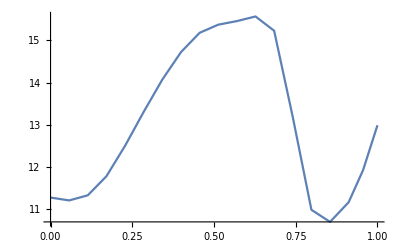

```mathematica
Plot[len[a],{a,0,1},MaxRecursion->1,PlotPoints->10]
```

在 a==0.8 附近时寻找弧长的最小值:

```mathematica
min=FindMinimum[len[a],{a,0.8},PrecisionGoal->5,AccuracyGoal->4]
```

{10.6871,{a→0.842411}}

## 多种数值函数的合并操作: 插值

通过预先计算来加速接下来的反复调用操作

从表面密度s(r)获得的球面对称的物体的密度 ρ(r) :

```mathematica
s[r_]:=10^-r^0.3
```

```mathematica
ρ[r_]/;r>0:=-1/π NIntegrate[D[s[t],t]/(√(t^2-r^2)),{t,r,∞}]
```

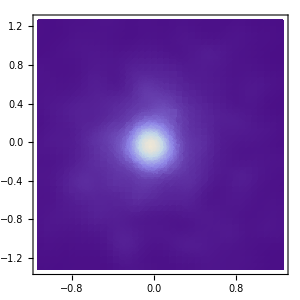
-Graphics3D--Graphics-

ρ(r) 是一个非常耗时的数值函数

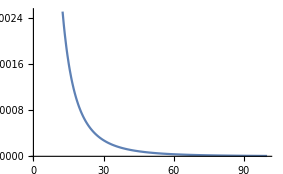
{1.51563,-Graphics-}

```mathematica
Timing[Plot[ρ[r],{r,1,100}]]
```

将 ρ(r) 在一个给定的范围上预先进行插值函数计算:

```mathematica
ρfunc=FunctionInterpolation[ρ[r],{r,1,100},MaxRecursion->10]
```

InterpolatingFunction[…]

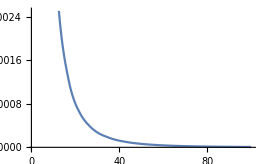
{0.015625,-Graphics-}

```mathematica
Timing[Plot[ρfunc[r],{r,1,100}]]
```

插值函数非常高效，可以用在更为复杂的函数当中

```mathematica
mass[r_]/;r>0:=NIntegrate[4π t^2 ρfunc[t],{t,0,r}]
```

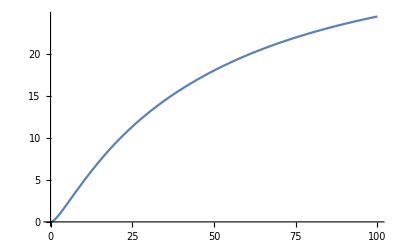

```mathematica
Plot[mass[r],{r,0,100}]
```

## 高效的内置函数

通常来讲最短的程序就是最快的程序

```mathematica
data=N[Range[10^6]];
```

手动生成的For循环相比而言非常缓慢:

```mathematica
Timing[For[i=1,i≤10^6,i++,Sin[data⟦i⟧]];]
```

内置函数非常快速:

```mathematica
Timing[Map[Sin, data];]
```

最快的程序一般是由内置可列表化的函数实现:

```mathematica
Timing[Sin[data];]
```

## 数字和数组: 在运算的早期使用机器精度数

精确输入得到精确输出，近似输入得到近似输出:

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Sin[x]+x
```

```mathematica
Nest[f,5,2]
```

近似已经得到的精确结果:

```mathematica
N[Nest[f,5,2]]
```

```mathematica
Nest[f,5.0,2]
```

可能会需要精确表达式:

```mathematica
N[Nest[f,5,2],50]
```

```mathematica
D[Nest[f,x,2],x]
```

如果你只需要近似的结果，最好在第一个输入数字的时候使用机器精度:

```mathematica
N[Nest[f,5,20]]//Timing
```

```mathematica
Nest[f,5.,20]//Timing
```

## 数字和数组: 封装数组

由机器精度数构成的列表和数组 (real, complex, integer) 可由Mathematica内部算法存储为封装数组.

Mathematica 可以自动生成封装数组:

```mathematica
packed=RandomReal[1,{10^7}];
```

```mathematica
unpacked=Developer`FromPackedArray[packed];
```

封装数组占用更少的内存:

```mathematica
ByteCount[packed]
```

```mathematica
ByteCount[unpacked]
```

封装数组运行速度更快:

```mathematica
Sin[packed];//Timing
```

```mathematica
Sin[unpacked];//Timing
```

## 数字和数组: 封装数组

对所有元素进行封装来优化机器精度数构成的数组

```mathematica
v=RandomReal[1,{10^6}];
```

封装数组对应的警告和报错信息:

```mathematica
On["Packing"];
```

机器精度数组中如果加入精确数，那么列表马上就封装解除:

```mathematica
v[[3]]=0;
```

```mathematica
Exp[v];//Timing
```

如果加入的是机器精度的数，列表马上又被转换成封装数组:

```mathematica
v[[3]]=0.;
```

```mathematica
Exp[v];//Timing
```

关闭信息:

```mathematica
Off["Packing"];
```

## 编译

编译生成一个高效运行的函数，但是仅能够使用机器精度的输入值

```mathematica
f=
Compile[{{c,_Complex}},Module[{i=1},FixedPoint[(i++;#^2+c)&,0,50,SameTest->(Re[#]^2+Im[#]^2≥4&)];i],
	CompilationTarget->"C",
	RuntimeAttributes->{Listable}];
```

Compile 产生虚拟机指令和二进制机器代码

```mathematica
InputForm[f]
```

被编译的函数可以快速运算并且可视化:

```mathematica
ArrayPlot[f[Table[x+ⅈ y,{x,-2.1,0.7,0.005},{y,-1.3,1.3,0.005}]],ColorFunction->"GreenPinkTones"]
```

放大 ( CompilationTarget 有相应的互动案例):

```mathematica
ArrayPlot[f[Table[x+ⅈ y,{x,0,0.5,0.001},{y,0.3,1,0.001}]],ColorFunction->"GreenPinkTones"]
```

## 编译: 自动优化

Mathematica 在很多情况下会自动编译，因此一般来讲不需要额外的手动操作

```mathematica
Table[x^2+Cos[x^2],{x,0,1,0.001}];
```

```mathematica
Plot[1/(2+Sin[x]),{x,0,5}]
```

```mathematica
NDSolve[{Sin[x]+y'[x]==Cos[y[x]],y[0]==0},y,{x,0,3}];
```

这种情况下Mathematica并不能检测出隐藏的可被编译的表达式:

```mathematica
Clear[f];
```

```mathematica
f[x_]/;NumberQ[x]=Integrate[1/(1+x^4),x]
```

```mathematica
Table[f[x],{x,0,1,0.0001}];//Timing
```

这种情况下手动编译有速度上的优势

```mathematica
compiled=Compile[{x},Evaluate[Integrate[1/(1+x^4),x]]];
```

```mathematica
g[x_]/;NumberQ[x]:=compiled[x]
```

```mathematica
Table[g[x],{x,0,1,0.0001}];//Timing
```

结论

更多学习资源

Functions and methods: Mathematica’s advanced tutorials

Examples: “Applications” in each documentation page; Wolfram Blog

Advanced development & debugging: Wolfram Workbench

## 初始化

Color

```mathematica
m8red[a_]:=RGBColor[0.811765,0.117647,0.145098,a];
```

C Compiler

```mathematica
Needs["CCodeGenerator`"]
```

Special Cells

```mathematica
PicturePrint[expr_,opts:OptionsPattern[Cell]]:=CellPrint[TextCell[expr,"Picture",opts,ShowStringCharacters->False]]
```

```mathematica
OverviewMouseover[header_,subs_]:=CellPrint@Cell[BoxData[ToBoxes@Mouseover[Framed[Style[header,"OverviewSection"],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5],

Evaluate@If[subs=="",Framed[Style[header,"OverviewSection",White],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5,Background->m8red[1]],Row[{Framed[Style[header,"OverviewSection",White],FrameMargins->{{15,15},{5,5}},FrameStyle->None,RoundingRadius->5,Background->m8red[1]]," » ",Framed[Style[subs,"OverviewSection"],FrameMargins->{{15,15},{5,5}},FrameStyle->m8red[1],BoxFrame->2,RoundingRadius->5,Background->White]}]]]],"OverviewSection"]
```

```mathematica
LargeOverviewMouseover[header_,subs_]:=CellPrint@Cell[BoxData[ToBoxes@Mouseover[Framed[Style[header,"LargeOverviewSection"],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5],

Evaluate@If[subs=="",Framed[Style[header,"LargeOverviewSection",White],FrameMargins->{{15,15},{5,5}},BoxFrame->2,FrameStyle->None,RoundingRadius->5,Background->m8red[1]],Row[{Framed[Style[header,"LargeOverviewSection",White],FrameMargins->{{15,15},{5,5}},FrameStyle->None,RoundingRadius->5,Background->m8red[1]]," » ",Framed[Style[subs,"LargeOverviewSection"],FrameMargins->{{15,15},{5,5}},FrameStyle->m8red[1],BoxFrame->2,RoundingRadius->5,Background->White]}]]]],"LargeOverviewSection"]
```

```mathematica
MapThread[LargeOverviewMouseover,Transpose[{{"Numerical Functions","Overview and applications"},{"Numerical Methods","Detailed algorithm control"},{"Numbers","Precision and accuracy"},{"Techniques","Programming and performance"}}]];
```

Utility: CreateSpecialCell

```mathematica
CreateSpecialCell[expr_]:=CellPrint@Cell[BoxData@ToBoxes@expr,"Picture",CellAutoOverwrite->False]
```

```mathematica
CreateSpecialTraditionalFormCell[expr_]:=CellPrint@Cell[BoxData@ToBoxes[expr,TraditionalForm],"Picture",CellAutoOverwrite->False]
```

NIntegrate Interpolation

```mathematica
Block[{y={{0,1.01},{0.2,1.03},{0.4,0.93},{0.6,0.85},{0.8,0.72},{1,0.57}}},ListLinePlot[y,Filling->Axis,InterpolationOrder->3,Mesh->Full,PlotStyle->PointSize[Large]]//CreateSpecialCell]
```

NIntegrate path integral

```mathematica
Block[{path,f,z},
path[t_]:=2+Exp[ⅈ t];
f[z_]:=Sin[z]/(z-2)^3;
Show[Plot3D[Abs[f[x+ⅈ y]],{x,0.5,3.5},{y,-1.5,1.5},ColorFunctionScaling->False,ColorFunction->(Darker@Hue[Rescale[Arg[Sin[#+ⅈ #2]/(#+ⅈ #2-2)^3],{-π,π},{0,1}]]&),PlotRange->{Automatic,5},PlotPoints->50,PlotLabel->Style[HoldForm@(Sin[z]/(z-2)^3),14],AxesLabel->{Re[z],Im[z],Abs[z]},LabelStyle->14],ParametricPlot3D[Append[Through[{Re,Im}[path[t]]],Abs[f[path[t]]]],{t,0,2π},PlotStyle->{Dashing[{}],Yellow,AbsoluteThickness[5]}]]]//CreateSpecialCell
```

FindRoot plot

```mathematica
Plot[{Cos[Cos[x]],x},{x,0,1},Epilog->{Red,PointSize[0.03],Point[{0.7390851332151608,0.7390851332151608}]}]//CreateSpecialCell
```

NDSolve numerical indefinite integral

```mathematica
TraditionalForm[Style[HoldForm[f[x]==Integrate[Sin[Exp[t]],{t,0,x}]=="?"],Large]]//CreateSpecialTraditionalFormCell
```

1D Optimization plots

```mathematica
Plot[Exp[-x^2] Cos[5Exp[x]],{x,-2,2},Epilog->{Red,PointSize[Large],Point[Reverse@MapAt[Composition[Last,Last],FindMinimum[Exp[-x^2] Cos[5Exp[x]],{x,1}],2]]}]//CreateSpecialCell
```

```mathematica
Plot[Exp[-x^2] Cos[5Exp[x]],{x,-2,2},Epilog->{Red,PointSize[Large],Point[Reverse@MapAt[Composition[Last,Last],NMinimize[{Exp[-x^2] Cos[5Exp[x]]},x],2]]}]//CreateSpecialCell
```

NMinimize constrained multidimensional

```mathematica
Block[{z,xy},
{z,xy}=NMinimize[{Sin[x]Cos[2y+1],x^4+y^2<3},{x,y}];
p=Show[Plot3D[Sin[x]Cos[2y+1],{x,-2,2},{y,-2,2},RegionFunction->({x,y}↦x^4+y^2<3),MeshFunctions->{#3&},AxesLabel->{x,y}],Graphics3D[{Red,PointSize[0.05],Point[{x,y,z}/.xy]}]]
]//CreateSpecialCell
```

MonteCarlo sampling points

```mathematica
Block[{pts=Last[Last[Reap[NIntegrate[Boole[x^2+y^2<1],{x,-1,1},{y,-1,1},Method->"AdaptiveMonteCarlo",EvaluationMonitor:>Sow[{x,y}],PrecisionGoal->2]]]],in,out},
in=Select[pts,(Norm[#]<1)&];
out=Complement[pts,in];RegionPlot[x^2+y^2<1,{x,-1,1},{y,-1,1},Epilog->{Red,Point[in],Lighter[Gray],Point[out]},PlotLabel->Style[x^2+y^2<1,16]]]//CreateSpecialCell
```

Sparse arrays 2D heat equation

```mathematica
Clear[q,x,y,u]
CreateSpecialTraditionalFormCell[Style[Row[{HoldForm[D[u,{x,2}]+D[u,{y,2}]==q],"⟹",HoldForm[(Subscript[u, i-1,j]-2 Subscript[u, i,j]+Subscript[u, i+1,j])+(Subscript[u, i,j-1]-2 Subscript[u, i,j]+Subscript[u, i,j+1])==q]},Spacer[30]],20]]
```

```mathematica
Graphics[{Opacity[0.3],Orange,Rectangle[{2,2}],{Opacity[1],Black,Inset[Style[TraditionalForm[-4 Subscript[u, i,j]],18],{2.5,2.5}]},Blue,Table[Rectangle[p],{p,{{1,2},{3,2},{2,1},{2,3}}}],{Opacity[1],Black,{Inset[Style[TraditionalForm[HoldForm[+Subscript[u, i-1,j]]],18],{1.5,2.5}],Inset[Style[TraditionalForm[+Subscript[u, i+1,j]//HoldForm],20],{3.5,2.5}],Inset[Style[TraditionalForm[+Subscript[u, i,j-1]//HoldForm],20],{2.5,1.5}],Inset[Style[TraditionalForm[+Subscript[u, i,j+1]//HoldForm],20],{2.5,3.5}]}}},PlotRange->{{0,6},{0,6}},ImageSize->{400,400},GridLines->{Range[0,6],Range[0,6]}]//CreateSpecialCell
```

NMinimize “RandomSearch” with large “SearchPoints”

```mathematica
Block[{x,y,z,xy,p},
{z,xy}=NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"RandomSearch","SearchPoints"->250}];
p=Show[Plot3D[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,-0.4,0.4},{y,-0.8,0},PlotPoints->50],Graphics3D[{Red,PointSize[0.05],Point[{x,y,z}/.xy]}]]
]//CreateSpecialCell
```

Spherically symmetric point cloud

```mathematica
Block[{data=Block[{n=1000},RandomVariate[ProbabilityDistribution[1/(r+1),{r,0,10}],n]Normalize/@RandomVariate[NormalDistribution[],{n,3}]]},Row[{Graphics3D[{Opacity[0.5],White,Point[data]},ViewPoint->{0,0,10},ViewVertical->{0,1,0},Background->Black,ImageSize->300,SphericalRegion->True],SmoothDensityHistogram[Take[data,All,2],ImageSize->300]},Spacer[20]]]//CreateSpecialCell
```

Utility: CreatePictureRowCell

```mathematica
CreatePictureGridCell[exprs_List,height_]:=CreateSpecialCell[Style[Grid[Map[Image[ImageResize[#,{Automatic,height}],ImageSize->All]&,exprs,{2}],Spacings->{1,1}]]]
```

Numerics functions

```mathematica
CreatePictureGridCell[{{Block[{path,f,z},
path[t_]:=2+Exp[ⅈ t];
f[z_]:=Sin[z]/(z-2)^3;
Show[Plot3D[Abs[f[x+ⅈ y]],{x,0.5,3.5},{y,-1.5,1.5},ColorFunctionScaling->False,ColorFunction->(Darker@Hue[Rescale[Arg[Sin[#+ⅈ #2]/(#+ⅈ #2-2)^3],{-π,π},{0,1}]]&),PlotRange->{Automatic,5},PlotPoints->50,LabelStyle->14],ParametricPlot3D[Append[Through[{Re,Im}[path[t]]],Abs[f[path[t]]]],{t,0,2π},PlotStyle->{Dashing[{}],Yellow,AbsoluteThickness[5]}]]],Block[{z,xy},
{z,xy}=NMinimize[{Sin[x]Cos[2y+1],x^4+y^2<3},{x,y}];
p=Show[Plot3D[Sin[x]Cos[2y+1],{x,-2,2},{y,-2,2},RegionFunction->({x,y}↦x^4+y^2<3),MeshFunctions->{#3&},AxesLabel->{x,y}],Graphics3D[{Red,PointSize[0.05],Point[{x,y,z}/.xy]}]]
],-Graphics-},{Block[{x,y,z},{x,y,z}={(2+Cos[v])Cos[u],(2+Cos[v])Sin[u],Sin[v](5/4-Cos[u])};
ParametricPlot3D[{x,y,z},{u,0,2π},{v,0,2π}]],Plot[Evaluate[{x[t],x'[t]}/.First[NDSolve[{x'[t]==x[t](x[t-Pi]-x'[t-1]),x[t/;t≤0]==Cos[t]},x,{t,0,5}]]],{t,0,5}],MatrixPlot[SparseArray[{{4,2}|{3,6}->4,{i_,i_}->2},{8,8}]]}},150]
```

Numerical methods

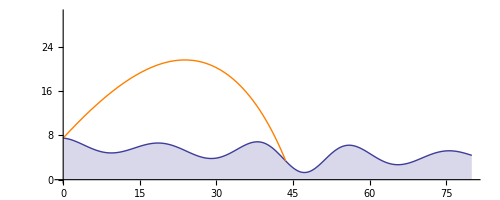
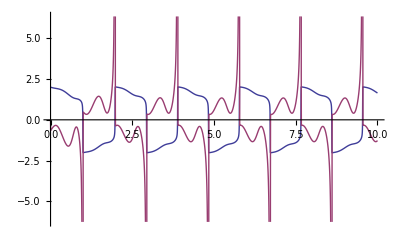
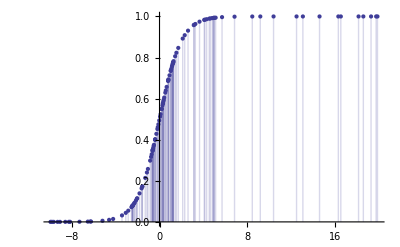
```mathematica
CreatePictureGridCell[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},150]
```

Techniques

```mathematica
CreatePictureGridCell[{{-Graphics-,-Graphics-}},250]
```

Lastly

```mathematica
$Line=0;
```